# user input

```mathematica
BPM=
100;
TimeSignature=
"4/4";
Complexity=
"Normal";
SoloInstrument=
"NewAge";
BackInstrument=
"NewAge";
ChordProgression=
{
"B Minor","B Minor","A Major","A Major","E Major","E Major","FSharp Minor","CSharp Major7"
};
Repetition=
1;
```

# random compose

```mathematica
AllowedTimes[Complexity_]:=
If[Complexity=="Simple",
{
Whole,Half,Quarter
},
If[Complexity=="Normal",
{
Whole,Half,Quarter,Eighth
},
If[Complexity=="Advanced",
{
Whole,Half,QuarterDot,Quarter,Eighth,Sixteenth,EighthTriplet,SixteenthTriplet
}
]
]
]
AllowedTimesValues[Complexity_]:=
If[Complexity=="Simple",
{
1,1/2,1/4
},
If[Complexity=="Normal",
{
1,1/2,1/4,1/8
},
If[Complexity=="Advanced",
{
1,1/2,3/8,1/4,1/8,1/16,1/8 2/3,1/16  2/3
}
]
]
]
AllowedTimesRules[expr_,Complexity_]:=
expr/.
ToRules[AllowedTimes[Complexity]==AllowedTimesValues[Complexity]]
CombineToQuarter[expr_]:=
expr/.
QuarterDot->{QuarterDot,Eighth}/.
EighthTriplet->ConstantArray[EighthTriplet,3]/.
SixteenthTriplet->ConstantArray[SixteenthTriplet,6]/.
Sixteenth->ConstantArray[Sixteenth,4]/.
Eighth->ConstantArray[Eighth,2]//
Flatten
GetOneMeasure[TimeSignature_,Complexity_]:=
Module[
{arr,s,i,arr2},
arr=
RandomChoice[AllowedTimes[Complexity],16]//
CombineToQuarter//
AllowedTimesRules[#,Complexity]&;
s=
0;
i=
1;
While[
s<ToExpression[TimeSignature],
If[arr[[i]]<=ToExpression[TimeSignature],
s=
s+arr[[i]]
];
i=
i+1
];
arr2=
arr[[1;;i-1]];
If[Total[arr2]>ToExpression[TimeSignature],
arr2[[-1]]=
arr2[[-1]]+ToExpression[TimeSignature]-Total[arr2]
];
Return[If[FreeQ[Positive/@arr2,False],arr2,GetOneMeasure[TimeSignature,Complexity]]]
]
MultiOctaves[]:=
ConstantArray[
{"A","BFlat","B","C","CSharp","D","DSharp","E","F","FSharp","G","GSharp"},
3
]//
Flatten
MajorRules[]:=
1+{0,2,4,5,7,9,11}
Major7Rules[]:=
1+{0,2,4,5,7,9,10}
Major7MajorRules[]:=
1+{0,2,4,5,7,9,11}
MinorRules[]:=
1+{0,2,3,5,7,8,10}
Minor7Rules[]:=
1+{0,2,3,5,7,8,10}
MajorChordRules[]:=
1+{0,7,12,16}
MinorChordRules[]:=
1+{0,7,12,15}
Major7ChordRules[]:=
1+{0,7,10,16}
Major7MajorChordRules[]:=
1+{0,7,11,16}
Minor7ChordRules[]:=
1+{0,7,10,15}
FormChord[Root_,Type_]:=
Module[
{arr,r},
arr=
MultiOctaves[][[
(Position[MultiOctaves[],Root]//Flatten//First);;(Position[MultiOctaves[],Root]//Flatten//Last)
]][[#]]&/@ToExpression[Type<>"ChordRules"][];
r=
{arr[[1]]<>"2",arr[[2]]<>"2",arr[[3]]<>"3",arr[[4]]<>"3"};
Return[r]
]
FormScale[Root_,Type_]:=
Module[
{octaves,first,second,last},
octaves=
MultiOctaves[][[
(Position[MultiOctaves[],Root]//Flatten//First);;(Position[MultiOctaves[],Root]//Flatten//Last)
]];
first=
(#<>"4"&/@octaves[[1;;-2]])[[#]]&/@ToExpression[Type<>"Rules"][];
second=
(#<>"5"&/@octaves[[1;;-2]])[[#]]&/@ToExpression[Type<>"Rules"][];
last=
{octaves[[1]]<>"6"};
Return[Join[first,second,last]]
]
```

```mathematica
Do[
RandomMeasure[]=
Table[
GetOneMeasure[TimeSignature,Complexity],
{t,Range[Length[ChordProgression]]}
];
RandomNotes[]=
RandomChoice[
FormScale[StringSplit[ChordProgression[[#]]," "][[1]],StringSplit[ChordProgression[[#]]," "][[2]]],
Length[RandomMeasure[][[#]]]
]&/@Range[Length[RandomMeasure[]]];
CompositionTableM[i]=
Flatten[
{
Table[
SoundNote[
RandomNotes[][[m]][[#]],
4 60/BPM RandomMeasure[][[m]][[#]],
SoloInstrument
]&/@Range[Length[RandomNotes[][[m]]]],
{m,Range[Length[ChordProgression]]}
],
Table[
SoundNote[
FormChord[
StringSplit[ChordProgression[[b]]," "][[1]],
StringSplit[ChordProgression[[b]]," "][[2]]],
{(b-1+(i-1)Length[ChordProgression])4 60/BPM ToExpression[TimeSignature],(b+(i-1)Length[ChordProgression]) 4 60/BPM ToExpression[TimeSignature]},
BackInstrument
],
{b,Range[Length[ChordProgression]]}
]
}
],
{i,Range[Repetition]}
]
CompositionTable=
Flatten[CompositionTableM/@Range[Repetition]];
```

# listen

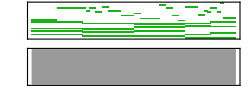

```mathematica
RandomComposition=
Sound[CompositionTable]
```